(Ay-By)/(Ax-Bx)==(Cy-Dy)/(Cx-Dx)

(-Ay+(Ax (Ay-By))/(Ax-Bx)+Cy-(Cx (Cy-Dy))/(Cx-Dx))/((Ay-By)/(Ax-Bx)-(Cy-Dy)/(Cx-Dx))

Ay+((Ay-By) (-Ax+(-Ay+(Ax (Ay-By))/(Ax-Bx)+Cy-(Cx (Cy-Dy))/(Cx-Dx))/((Ay-By)/(Ax-Bx)-(Cy-Dy)/(Cx-Dx))))/(Ax-Bx)

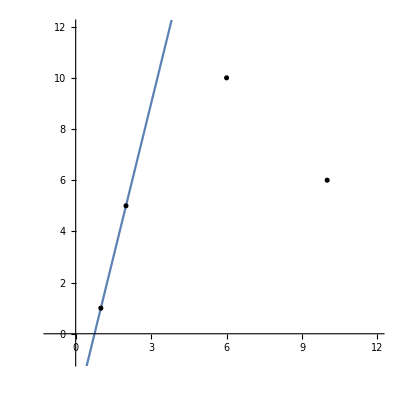

```mathematica
ClearAll["Global`*"];
nRad=.1;
pA={Ax,Ay};
pB={Bx,By};
pC={Cx,Cy};
pD={Dx,Dy};
m1=(Ay-By)/(Ax-Bx);
m2=(Cy-Dy)/(Cx-Dx);
m1==m2
y1[x_]:=(Ay-By)/(Ax-Bx)(x-Ax)+Ay;
y2[x_]:=(Cy-Dy)/(Cx-Dx)(x-Cx)+Cy;
S=Solve[y1[x]==y2[x],x];
Sx=S[[1]][[1]][[2]]
Sy=y1[Sx]

{Ax,Ay}={1, 1};
{Bx,By}={2, 5};
{Cx,Cy}={6, 10};
{Dx,Dy}={10, 6};
dA=Graphics[{Black,Disk[pA,nRad]}];
dB=Graphics[{Black,Disk[pB,nRad]}];
dC=Graphics[{Black,Disk[pC,nRad]}];
dD=Graphics[{Black,Disk[pD,nRad]}];
g1=Plot[y1[x],{x,-1,11}];
Show[g1,
dA,dB,dC,dD,
Axes->True,
AspectRatio->Automatic,
PlotRange->{{-1,12},{-1,12}}
]
```

```mathematica
(Ay-By)/(Ax-Bx)==(Cy-Dy)/(Cx-Dx)
(Ay-By)(Cx-Dx)==(Cy-Dy)*Ax-Bx
```

```mathematica
(-Ay+Ax m1+Cy-Cx m2)/(m1-m2)
```